```mathematica
Needs["ErrorBarPlots`"]
```

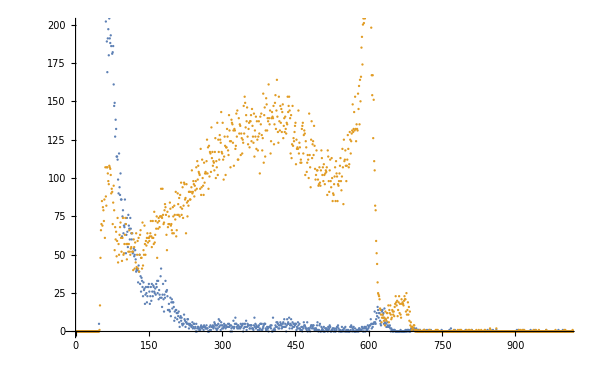

```mathematica
imp=Import[NotebookDirectory[]<>"../data/part3/Co-Si.mca","Table"];
data=Flatten[Drop[Drop[imp,12],-1]];
data=Table[{i,data[[i]]},{i,1,Length[data]}];
imp2=Import[NotebookDirectory[]<>"../data/part3/Co-CdTe.mca","Table"];
data2=Flatten[Drop[Drop[imp2,12],-1]];
ListPlot[{data,data2},PlotRange->{{0,1000},{0,200}}]
```

42

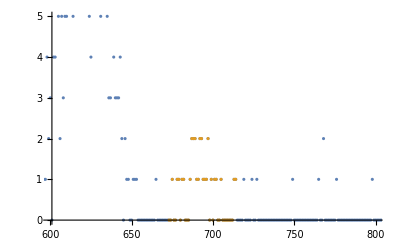

```mathematica
start=672;
end=714;
datacut=Drop[Drop[data,start],-(Length[data]-end)];
Length[datacut]
ListPlot[{data,datacut},PlotRange->{{600,800},{0,5}}]
```

{{674,1/4,1/8},{678,1/2,1/(4 √2)},{682,1/2,1/(4 √2)},{686,5/4,(√5)/8},{690,3/2,(√(3/2))/4},{694,5/4,(√5)/8},{698,3/4,(√3)/8},{702,1/2,1/(4 √2)},{706,1/4,1/8},{710,0,0}}

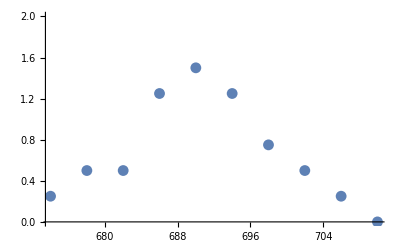

```mathematica
bin=4;
datacutsum=Table[{start+i bin -bin/2,Sum[datacut[[bin i-n,2]],{n,0,bin-1}]/bin,√(Sum[datacut[[bin i-n,2]],{n,0,bin-1}]/bin)*1/bin},{i,1,Floor[Length[datacut]/bin]}]
ListPlot[datacutsum[[All,{1,2}]],PlotRange->{Automatic,{0,2}}]
```

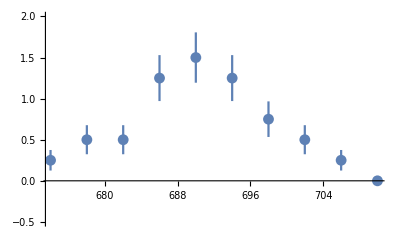

```mathematica
ErrorListPlot[Table[{{datacutsum[[i,1]],datacutsum[[i,2]]},ErrorBar[datacutsum[[i,3]]]},{i,1,Length[datacutsum]}],PlotRange->{-0.5,2}]
```

```mathematica
Export[NotebookDirectory[]<>"../calc/part3/Co-Si_mergedbins.txt",datacutsum//N,"Table"]
```

/home/moritz/FP1/1002-Halbleiter/src/../calc/part3/Co-Si_mergedbins.txt